```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["stats.out"];
graphtitle="Base hosts file size";
```

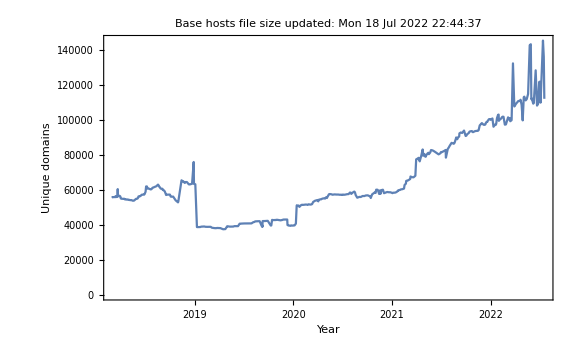

```mathematica
graph=DateListPlot[({DateObject[#1⟦1⟧],#1⟦2⟧}&)/@data
,PlotTheme->"Detailed"
,FrameLabel->{{HoldForm[Unique domains],None},{HoldForm[Year],None}}
,FrameTicks->{{All,All},Automatic}
,ImageMargins->20
,ImageSize -> Large
,PlotLabel -> 
Column[
{
Style[graphtitle,16,Bold]
,Style["updated: "<>DateString[],12]
}
,Center
]
,LabelStyle->{GrayLevel[0]}
];
Export[StringReplace[ToLowerCase[graphtitle]," "->"_"]<> ".png", graph];
graph
```